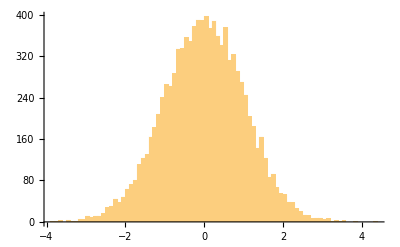

DataDistribution[…]

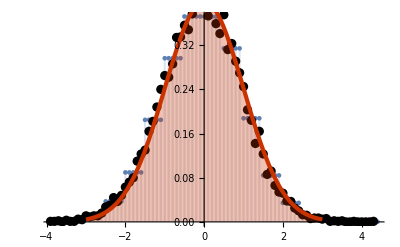

```mathematica
dat = RandomVariate[NormalDistribution[],10^4];
hl=HistogramList[dat,100];
Histogram[dat,{hl[[1]]}]
d=HistogramDistribution[dat]
dp1:=DiscretePlot[PDF[d,x],{x,hl[[1]]}]
dp2:=Plot[PDF[NormalDistribution[],x],{x,-3,3},Filling->Axis,PlotTheme->"Web"]
x = hl[[1]];
y = hl[[2]]/Total[hl[[2]]*Differences[hl[[1]]]];
dp3 := ListPlot[Partition[Riffle[x,y],2],PlotStyle->Black]

Show[dp1,dp3,dp2]
```

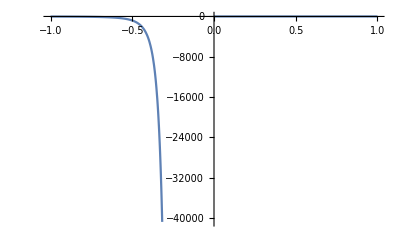

```mathematica
Plot[Exp[-3/x]/x,{x,-1,1}]
```